```mathematica
data =Import["C:\\Users\\Juhász Nóra\\Documents\\GitHub\\ABM-PDE\\StochasticVariability\\theo_results\\theo3.txt", "Table"];
```

dataLength will be 1000, this was just an experiment

```mathematica
dataLength=1000;
```

```mathematica
cleanData={};
```

```mathematica
For[i=1,i<=dataLength, i++,cleanData=Append[cleanData,data[[i]][[4]]]]
```

```mathematica
cleanData;
```

```mathematica
probabilityData={};
```

```mathematica
For[i=0,i<=Max[cleanData], i++,probabilityData=Append[probabilityData,{i,0}]]
```

```mathematica
probabilityData
```

{{0,0},{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0},{12,0},{13,0},{14,0},{15,0},{16,0},{17,0},{18,0},{19,0},{20,0},{21,0},{22,0},{23,0},{24,0},{25,0},{26,0},{27,0},{28,0},{29,0},{30,0},{31,0},{32,0},{33,0},{34,0},{35,0},{36,0},{37,0},{38,0},{39,0},{40,0},{41,0},{42,0},{43,0},{44,0},{45,0},{46,0},{47,0},{48,0},{49,0},{50,0},{51,0}}

```mathematica
For[i=1,i<=dataLength, i++,probabilityData[[cleanData[[i]]+1,2]]=probabilityData[[cleanData[[i]]+1,2]] + 1]
```

```mathematica
probabilityData
```

{{0,114},{1,121},{2,97},{3,82},{4,93},{5,67},{6,65},{7,40},{8,34},{9,28},{10,28},{11,28},{12,31},{13,25},{14,17},{15,12},{16,18},{17,11},{18,13},{19,12},{20,8},{21,7},{22,10},{23,3},{24,9},{25,3},{26,2},{27,3},{28,2},{29,3},{30,1},{31,1},{32,0},{33,1},{34,3},{35,2},{36,1},{37,0},{38,3},{39,0},{40,0},{41,0},{42,0},{43,1},{44,0},{45,0},{46,0},{47,0},{48,0},{49,0},{50,0},{51,1}}

```mathematica
N[Sum[probabilityData[[i,1]]*probabilityData[[i,2]]/1000,{i,1,Length[probabilityData]}]]
```

6.775

```mathematica
probDensFunc[x_]:=N[probabilityData[[x+1,2]]/dataLength]
```

```mathematica
probDensFunc[0]
```

0.114

http://math.bme.hu/~nandori/Virtual_lab/stat/expect/Generating.pdf

```mathematica
probGenFunc[z_]:=Sum[probDensFunc[n]*(z^n),{n,0,Max[cleanData]}]
```

```mathematica
probGenFunc[0.01]
```

0.11522

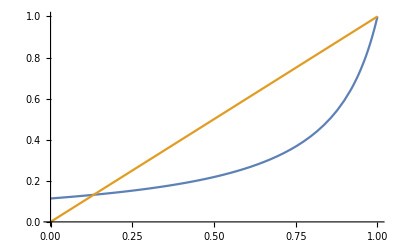

```mathematica
Plot[{probGenFunc[t],t},{t,0,1}]
```

```mathematica
probGenFunc[0.2687]
```

0.155715

```mathematica
cleanData;
```

```mathematica
DistributionFitTest[cleanData,GeometricDistribution[probabilityData[[1,2]]/1000],"HypothesisTestData"]["TestDataTable",All]
```

| Statistic | P-Value
Pearson χ^2 | 34.2772 | 0.017041

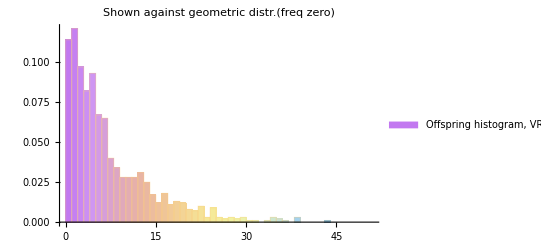

```mathematica
p1=Histogram[cleanData,{0,Max[cleanData],1},"Probability",ChartLegends->{"Offspring histogram, VRR=1.67*E-3."},ChartStyle->"Pastel",PlotLabel->"Shown against geometric distr.(freq zero)"]
```

```mathematica
probabilityData[[1,2]]
```

114

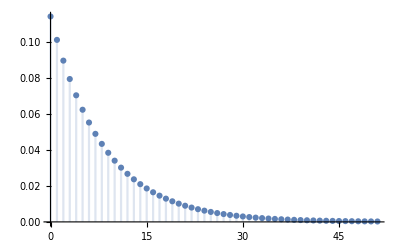

```mathematica
p2=DiscretePlot[PDF[GeometricDistribution[probabilityData[[1,2]]/1000],x]//Evaluate,{x,0,Max[cleanData]},PlotMarkers->Automatic]
```

```mathematica
Rasterize[Show[p1,p2]]
```

-Graphics-